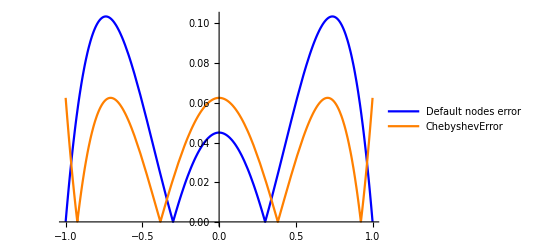

```mathematica
f[x_] = Log[x^2 + 1];
nodes = {-1, -0.3, 0.3, 1};
values = Map[f, nodes];
l[num_, x_, nodes_, values_] := Product[If[num  ≠ i ,(x - nodes[[i]]) / (nodes[[num ]] - nodes[[i]]), 1], {i, 1, Length[nodes]}] ;
L[x_, nodes_, values_] := Sum[l[i, x, nodes, values] * values[[i]], {i, 1, Length[values]}];
Cheb[k_, n_] = Cos[((2k - 1)/(2n) )Pi];
ChebNodes = Table[Cheb[i, Length[nodes]], {i, 1, Length[nodes]}];
ChebValues = Map[f, ChebNodes];
LDefault[x_] = L[x, nodes, values];
LChebyshev[x_] = L[x, ChebNodes, ChebValues];
Deriv[ksi_]= D[f[x], {x, Length[nodes]}] /.{x->ksi};
Error[xi_, x_] :=Deriv[xi]/Length[nodes]!Product[x - nodes[[i]], {i, 1, Length[nodes]}];
xi  = x /. NMaximize[{Abs[Deriv[x]], -1≤x≤1}, x ] [[2]];
ChebError[xi_, x_] :=Deriv[xi]/Length[ChebNodes]! Product[x-ChebNodes[[i]], {i, 1, Length[ChebNodes]}];
Plot[{Abs[Error[xi, x]], Abs[ChebError[xi, x]]}, {x, -1, 1}, PlotStyle->{Blue, Orange}, PlotLegends->{"Default nodes error", "ChebyshevError"}]
```

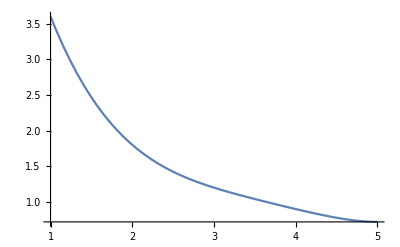

{{x→2.54203},{x→3.15308-2.14365 ⅈ},{x→3.15308+2.14365 ⅈ},{x→6.1518}}

```mathematica
nodes2 = {1, 2, 3, 4, 5};
values2 = {3.6, 1.8, 1.2, 0.9, 0.72};
L2[x_] = L[x, nodes2, values2];
Plot[L2[x], {x, 1, 5}]
Solve[L2[x] == 1.4, x]
1≤2.542033787366703≤5
```

```mathematica
CustomSum[expression_, {variable_, start_, end_}] = SumHelper[expression, 0, {variable, start, end}];
SumHelper[expression_, sum_, {variable_, start_, end_}] = If[start > end, sum,  SumHelper[expression, sum + expression /. variable->start, {x, start + 1, end}]];

x[i_] = x0 + i h;
FiniteDifference[f_,k_, i_] := If[k == 0, 1, If[k == 1, (f[x]/.x->x[i + 1])- (f[x]/.x->x[i]),
FiniteDifference[f, k -1, i + 1] - FiniteDifference[f, k -1, i]]];
FiniteDifference[f, 1, 0]
NewtonForward[n_, x0_, f_, x_] := CustomSum[Binomial[n, k] *FiniteDifference[f, k, 0], {k, 0, n}];
```

```mathematica
fi[i_] = f[x]/.x->x0+i h;
f[x] = 1/(x*x*x);
y[x]  = 1/(x*x);

FiniteDifference[f_,k_, i_, x0, h] := If[k == 0, 1, If[k == 1, (f[x]/.x->x[i + 1])- (f[x]/.x->x[i]),
FiniteDifference[f, k -1, i + 1] - FiniteDifference[f, k -1, i]]]
FiniteDifference[f, 1, 0, 1, 10]
```

Syntax::tsntxi: "FiniteDifference[f_,k_,i_,x0,h]:=If[k==0,1,If[k==1,(f[x]/.x→x[i+1])-(f[x]/.x→x[i]),FiniteDifference[f,k-1,i+1]-FiniteDifference[f,k-1,i]]],x[index_]=x0+indexh,;" is incomplete; more input is needed.